```mathematica
PiRectangles[n_]:=Module[{pi,pts,i,t},
t=AbsoluteTime[];
pts=Table[0,{i,0,n}];
pi=RealDigits[Pi,10,n];
pi=pi[[1]];
For[i=1,i≤n,i++,
pts[[i+1]]=pts[[i]]+pi[[i]]*Exp[i*ⅈ*Pi/2];
];
pts=Table[{Re[pts[[i]]],Im[pts[[i]]]},{i,1,n+1}];
Print[AbsoluteTime[]-t];
Show[Graphics[Line[pts]]]
];
```

0.00826

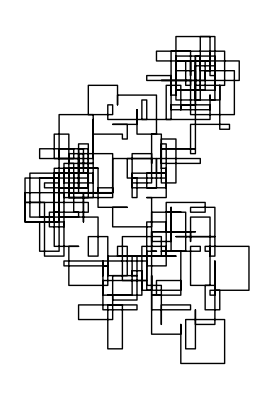

```mathematica
PiRectangles[500]
```